# Backward error analysis Symmetric Multistep methods on y’’[t] = ∇U[y[t]]

## Symmetric 7-step method (conjugate symplectic)

```mathematica
Clear["Global`*"]
```

dimension

```mathematica
dim = 2;
```

```mathematica
y = Function[t, Array[Subscript[x, #1][t]&,dim]]
```

Function[t,Array[x_#1[t]&,dim]]

```mathematica
symA[k_,d_] := Array[Subscript[a, #1,#2][k]&,{d,d}]/. Subscript[a, i_,j_][k] /; i>j -> Subscript[a, j,i][k]
```

## Construction

number of step-triples

```mathematica
nn=2;
```

consistency requirement: coefficients sum to identity matrix

```mathematica
aLast = 1/nn^2(IdentityMatrix[dim]-Sum[j^2 symA[j,dim],{j,1,nn-1}]);
```

```mathematica
aLast//MatrixForm
```

(1/4 (1-a_(1,1)[1]) | -1/4 a_(1,2)[1]
-1/4 a_(1,2)[1] | 1/4 (1-a_(2,2)[1]))

```mathematica
aLastSubst = Subscript[a, i_,j_][nn]:> aLast[[i,j]]
```

a_(i_,j_)[2]:>aLast⟦i,j⟧

```mathematica
meth = 1/h^2(Sum[symA[j,dim].(-2 y[t] + y[t + j h] + y[t - j h]),{j,1,nn}] ) -  D[U@@ y[t],{y[t]}] /.aLastSubst;
```

```mathematica
mth =Simplify[meth]
```

{(1/4 (-2 x_1[t]+x_1[-2 h+t]+x_1[2 h+t]) (1-a_(1,1)[1])+(-2 x_1[t]+x_1[-h+t]+x_1[h+t]) a_(1,1)[1]+(-2 x_2[t]+x_2[-h+t]+x_2[h+t]) a_(1,2)[1]-1/4 (-2 x_2[t]+x_2[-2 h+t]+x_2[2 h+t]) a_(1,2)[1])/h^2-U^(1,0)[x_1[t],x_2[t]],((-2 x_1[t]+x_1[-h+t]+x_1[h+t]) a_(1,2)[1]-1/4 (-2 x_1[t]+x_1[-2 h+t]+x_1[2 h+t]) a_(1,2)[1]+1/4 (-2 x_2[t]+x_2[-2 h+t]+x_2[2 h+t]) (1-a_(2,2)[1])+(-2 x_2[t]+x_2[-h+t]+x_2[h+t]) a_(2,2)[1])/h^2-U^(0,1)[x_1[t],x_2[t]]}

## Computation of modified equation y''[t] = ∇U[y[t]] + O[h]^2

order

```mathematica
o=4;
```

```mathematica
y2Ans = y2Ans = Subscript[x, k_]''[t]-> Sum[c[k,j]h^j,{j,0,o}]
```

x_k_''[t]→c[k,0]+h c[k,1]+h^2 c[k,2]+h^3 c[k,3]+h^4 c[k,4]

```mathematica
cVars = Flatten[Table[c[k,j],{j,0,o},{k,1,dim}]];
```

```mathematica
solveSeriesY2 = Solve[Series[mth,{h,0,o}]==0/.y2Ans,cVars]
```

{{c[1,0]→U^(1,0)[x_1[t],x_2[t]],c[2,0]→U^(0,1)[x_1[t],x_2[t]],c[1,1]→0,c[2,1]→0,c[1,2]→1/12 (-4 x_1^(4)[t]+3 a_(1,1)[1] x_1^(4)[t]+3 a_(1,2)[1] x_2^(4)[t]),c[2,2]→1/12 (3 a_(1,2)[1] x_1^(4)[t]-4 x_2^(4)[t]+3 a_(2,2)[1] x_2^(4)[t]),c[1,3]→0,c[2,3]→0,c[1,4]→1/360 (-16 x_1^(6)[t]+15 a_(1,1)[1] x_1^(6)[t]+15 a_(1,2)[1] x_2^(6)[t]),c[2,4]→1/360 (15 a_(1,2)[1] x_1^(6)[t]-16 x_2^(6)[t]+15 a_(2,2)[1] x_2^(6)[t])}}

```mathematica
y2 =  O[h]^(o+1)+D[y[t],{t,2}]/.y2Ans/.solveSeriesY2[[1]]
```

{U^(1,0)[x_1[t],x_2[t]]+1/12 (-4 x_1^(4)[t]+3 a_(1,1)[1] x_1^(4)[t]+3 a_(1,2)[1] x_2^(4)[t]) h^2+1/360 (-16 x_1^(6)[t]+15 a_(1,1)[1] x_1^(6)[t]+15 a_(1,2)[1] x_2^(6)[t]) h^4+O[h]^5,U^(0,1)[x_1[t],x_2[t]]+1/12 (3 a_(1,2)[1] x_1^(4)[t]-4 x_2^(4)[t]+3 a_(2,2)[1] x_2^(4)[t]) h^2+1/360 (15 a_(1,2)[1] x_1^(6)[t]-16 x_2^(6)[t]+15 a_(2,2)[1] x_2^(6)[t]) h^4+O[h]^5}

```mathematica
subsmthd = Derivative[j_][Subscript[x, k_]][t] /; j≥ 2:> D[Normal[y2[[k]]],{t,j-2}]
```

x_k_^(j_)[t]/;j≥2:>∂_{t,j-2} Normal[y2⟦k⟧]

```mathematica
y2Red = O[h]^(o+1)+D[y[t],{t,2}] //. subsmthd;
```

```mathematica
(*y2Red = Simplify[y2Red]*)
```

## Lagrangian of method

```mathematica
Ld =  1/(2 h^2)(Sum[ (y[t+j h]-y[t]).symA[j,dim].(y[t+j h]-y[t]),{j,1,nn}]) +U@@y[t] /.aLastSubst
```

U[x_1[t],x_2[t]]+1/(2 h^2)((-x_1[t]+x_1[h+t]) ((-x_1[t]+x_1[h+t]) a_(1,1)[1]+(-x_2[t]+x_2[h+t]) a_(1,2)[1])+(-x_1[t]+x_1[2 h+t]) (1/4 (-x_1[t]+x_1[2 h+t]) (1-a_(1,1)[1])-1/4 (-x_2[t]+x_2[2 h+t]) a_(1,2)[1])+(-x_2[t]+x_2[2 h+t]) (-1/4 (-x_1[t]+x_1[2 h+t]) a_(1,2)[1]+1/4 (-x_2[t]+x_2[2 h+t]) (1-a_(2,2)[1]))+(-x_2[t]+x_2[h+t]) ((-x_1[t]+x_1[h+t]) a_(1,2)[1]+(-x_2[t]+x_2[h+t]) a_(2,2)[1]))

```mathematica
LdS = Series[Ld,{h,0,o}];
```

### Verify that Lagrangian recovers method

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
elHigh = EulerEquations[LdS,y[t],t]
```

{(-x_1''[t]+U^(1,0)[x_1[t],x_2[t]])+1/12 ((-4+3 a_(1,1)[1]) x_1^(4)[t]+3 a_(1,2)[1] x_2^(4)[t]) h^2+1/360 ((-16+15 a_(1,1)[1]) x_1^(6)[t]+15 a_(1,2)[1] x_2^(6)[t]) h^4+O[h]^5==0,(-x_2''[t]+U^(0,1)[x_1[t],x_2[t]])+1/12 (3 a_(1,2)[1] x_1^(4)[t]+(-4+3 a_(2,2)[1]) x_2^(4)[t]) h^2+1/360 (15 a_(1,2)[1] x_1^(6)[t]+(-16+15 a_(2,2)[1]) x_2^(6)[t]) h^4+O[h]^5==0}

```mathematica
y2TestCs=Solve[elHigh/.y2Ans,cVars];
```

```mathematica
y2Test = O[h]^(o+1)+D[y[t],{t,2}]/.y2Ans/.y2TestCs[[1]];
```

```mathematica
(*y2Test=Expand[y2Test]*)
```

```mathematica
subsmthdTest = Derivative[j_][Subscript[x, k_]][t] /; j≥ 2:> D[Normal[y2Test[[k]]],{t,j-2}]
```

x_k_^(j_)[t]/;j≥2:>∂_{t,j-2} Normal[y2Test⟦k⟧]

```mathematica
y2TestRed = O[h]^(o+1)+D[y[t],{t,2}]//. subsmthdTest;
```

```mathematica
ass=Flatten[{#1 -> RandomInteger[10] & /@ Flatten[Table[symA[j,dim],{j,1,nn}]],U-> (Exp[#1+#2]&)}]
```

{a_(1,1)[1]→4,a_(1,2)[1]→6,a_(1,2)[1]→3,a_(2,2)[1]→7,a_(1,1)[2]→5,a_(1,2)[2]→8,a_(1,2)[2]→9,a_(2,2)[2]→9,U→(Exp[#1+#2]&)}

```mathematica
Simplify[y2Red-y2TestRed/.ass]
```

{O[h]^5,O[h]^5}

## Compute BEA Hamiltonian and Symplectic Structure

Find highest derivative of x in LdS

```mathematica
terms =Flatten[Apply[List,ExpandAll[Normal[LdS]],{0,1}]];
```

```mathematica
mx=Max[Cases[terms,Derivative[j_][Subscript[x, k_]][t]->j]]
```

5

q variables of Hamiltonian system on extended phase space

```mathematica
q=Flatten[Table[D[y[t],{t,i}],{i,0,mx-1}]]
```

{x_1[t],x_2[t],x_1'[t],x_2'[t],x_1''[t],x_2''[t],x_1^(3)[t],x_2^(3)[t],x_1^(4)[t],x_2^(4)[t]}

Conjugate momenta to q=(y,y’,...,y^(mx-1))
p[k] is the conjugate momentum to q[[k]]=y^(k-1)

```mathematica
p[k_]:= Sum[ (-1)^j D[D[LdS,#]& /@D[y[t],{t,j+k}],{t,j}],{j,0,mx-k}]
```

```mathematica
pFlat = Flatten[Table[p[k],{k,1,mx}]];
```

### Modified Hamiltonian on extended phase space

```mathematica
H = D[q,t].pFlat-LdS;
```

```mathematica
H=Simplify[H]
```

1/2 (-2 U[x_1[t],x_2[t]]+x_1'[t]^2+x_2'[t]^2)+1/24 ((-4+3 a_(1,1)[1]) x_1''[t]^2+6 a_(1,2)[1] x_1''[t] x_2''[t]+(-4+3 a_(2,2)[1]) x_2''[t]^2+8 x_1'[t] x_1^(3)[t]-6 a_(1,1)[1] x_1'[t] x_1^(3)[t]-6 a_(1,2)[1] x_2'[t] x_1^(3)[t]-6 a_(1,2)[1] x_1'[t] x_2^(3)[t]+8 x_2'[t] x_2^(3)[t]-6 a_(2,2)[1] x_2'[t] x_2^(3)[t]) h^2+1/720 ((16-15 a_(1,1)[1]) (x_1^(3)[t])^2-30 a_(1,2)[1] x_1^(3)[t] x_2^(3)[t]+(16-15 a_(2,2)[1]) (x_2^(3)[t])^2-32 x_1''[t] x_1^(4)[t]+30 a_(1,1)[1] x_1''[t] x_1^(4)[t]+30 a_(1,2)[1] x_2''[t] x_1^(4)[t]+30 a_(1,2)[1] x_1''[t] x_2^(4)[t]-32 x_2''[t] x_2^(4)[t]+30 a_(2,2)[1] x_2''[t] x_2^(4)[t]+32 x_1'[t] x_1^(5)[t]-30 a_(1,1)[1] x_1'[t] x_1^(5)[t]-30 a_(1,2)[1] x_2'[t] x_1^(5)[t]-30 a_(1,2)[1] x_1'[t] x_2^(5)[t]+32 x_2'[t] x_2^(5)[t]-30 a_(2,2)[1] x_2'[t] x_2^(5)[t]) h^4+O[h]^5

Remark. The symplectic structure on the extended phase space can be computed as dq ⋀ dp, if needed.

### Modified Hamiltonian on reduced phase space

```mathematica
HH = H //.subsmthd;
```

```mathematica
HH=Simplify[HH]
```

1/2 (-2 U[x_1[t],x_2[t]]+x_1'[t]^2+x_2'[t]^2)+1/24 ((-4+3 a_(2,2)[1]) (U^(0,1)[x_1[t],x_2[t]])^2+8 x_2'[t]^2 U^(0,2)[x_1[t],x_2[t]]-6 a_(2,2)[1] x_2'[t]^2 U^(0,2)[x_1[t],x_2[t]]+6 a_(1,2)[1] U^(0,1)[x_1[t],x_2[t]] U^(1,0)[x_1[t],x_2[t]]-4 (U^(1,0)[x_1[t],x_2[t]])^2+3 a_(1,1)[1] (U^(1,0)[x_1[t],x_2[t]])^2-6 a_(1,2)[1] x_2'[t]^2 U^(1,1)[x_1[t],x_2[t]]+x_1'[t]^2 (-6 a_(1,2)[1] U^(1,1)[x_1[t],x_2[t]]+2 (4-3 a_(1,1)[1]) U^(2,0)[x_1[t],x_2[t]])-2 x_1'[t] x_2'[t] (3 a_(1,2)[1] U^(0,2)[x_1[t],x_2[t]]+(-8+3 a_(1,1)[1]+3 a_(2,2)[1]) U^(1,1)[x_1[t],x_2[t]]+3 a_(1,2)[1] U^(2,0)[x_1[t],x_2[t]])) h^2+1/720 (-32 x_2'[t]^2 (U^(0,2)[x_1[t],x_2[t]])^2-45 (a_(1,2)[1])^2 x_2'[t]^2 (U^(0,2)[x_1[t],x_2[t]])^2+75 a_(2,2)[1] x_2'[t]^2 (U^(0,2)[x_1[t],x_2[t]])^2-45 (a_(2,2)[1])^2 x_2'[t]^2 (U^(0,2)[x_1[t],x_2[t]])^2-48 x_2'[t]^4 U^(0,4)[x_1[t],x_2[t]]-45 (a_(1,2)[1])^2 x_2'[t]^4 U^(0,4)[x_1[t],x_2[t]]+90 a_(2,2)[1] x_2'[t]^4 U^(0,4)[x_1[t],x_2[t]]-45 (a_(2,2)[1])^2 x_2'[t]^4 U^(0,4)[x_1[t],x_2[t]]-90 a_(1,2)[1] x_2'[t]^2 U^(0,3)[x_1[t],x_2[t]] U^(1,0)[x_1[t],x_2[t]]+45 a_(1,1)[1] a_(1,2)[1] x_2'[t]^2 U^(0,3)[x_1[t],x_2[t]] U^(1,0)[x_1[t],x_2[t]]+45 a_(1,2)[1] a_(2,2)[1] x_2'[t]^2 U^(0,3)[x_1[t],x_2[t]] U^(1,0)[x_1[t],x_2[t]]+60 a_(1,2)[1] x_2'[t]^2 U^(0,2)[x_1[t],x_2[t]] U^(1,1)[x_1[t],x_2[t]]-45 a_(1,1)[1] a_(1,2)[1] x_2'[t]^2 U^(0,2)[x_1[t],x_2[t]] U^(1,1)[x_1[t],x_2[t]]-45 a_(1,2)[1] a_(2,2)[1] x_2'[t]^2 U^(0,2)[x_1[t],x_2[t]] U^(1,1)[x_1[t],x_2[t]]-90 a_(1,2)[1] (U^(1,0)[x_1[t],x_2[t]])^2 U^(1,1)[x_1[t],x_2[t]]+45 a_(1,1)[1] a_(1,2)[1] (U^(1,0)[x_1[t],x_2[t]])^2 U^(1,1)[x_1[t],x_2[t]]+45 a_(1,2)[1] a_(2,2)[1] (U^(1,0)[x_1[t],x_2[t]])^2 U^(1,1)[x_1[t],x_2[t]]-32 x_2'[t]^2 (U^(1,1)[x_1[t],x_2[t]])^2-15 a_(1,1)[1] x_2'[t]^2 (U^(1,1)[x_1[t],x_2[t]])^2-45 (a_(1,2)[1])^2 x_2'[t]^2 (U^(1,1)[x_1[t],x_2[t]])^2+90 a_(2,2)[1] x_2'[t]^2 (U^(1,1)[x_1[t],x_2[t]])^2-45 (a_(2,2)[1])^2 x_2'[t]^2 (U^(1,1)[x_1[t],x_2[t]])^2+(U^(0,1)[x_1[t],x_2[t]])^2 ((48+45 (a_(1,2)[1])^2-90 a_(2,2)[1]+45 (a_(2,2)[1])^2) U^(0,2)[x_1[t],x_2[t]]+45 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(1,1)[x_1[t],x_2[t]])-96 x_2'[t]^2 U^(1,0)[x_1[t],x_2[t]] U^(1,2)[x_1[t],x_2[t]]-90 a_(1,1)[1] x_2'[t]^2 U^(1,0)[x_1[t],x_2[t]] U^(1,2)[x_1[t],x_2[t]]+45 (a_(1,1)[1])^2 x_2'[t]^2 U^(1,0)[x_1[t],x_2[t]] U^(1,2)[x_1[t],x_2[t]]-90 (a_(1,2)[1])^2 x_2'[t]^2 U^(1,0)[x_1[t],x_2[t]] U^(1,2)[x_1[t],x_2[t]]+270 a_(2,2)[1] x_2'[t]^2 U^(1,0)[x_1[t],x_2[t]] U^(1,2)[x_1[t],x_2[t]]-135 (a_(2,2)[1])^2 x_2'[t]^2 U^(1,0)[x_1[t],x_2[t]] U^(1,2)[x_1[t],x_2[t]]+90 a_(1,2)[1] x_2'[t]^4 U^(1,3)[x_1[t],x_2[t]]-45 a_(1,1)[1] a_(1,2)[1] x_2'[t]^4 U^(1,3)[x_1[t],x_2[t]]-45 a_(1,2)[1] a_(2,2)[1] x_2'[t]^4 U^(1,3)[x_1[t],x_2[t]]+48 (U^(1,0)[x_1[t],x_2[t]])^2 U^(2,0)[x_1[t],x_2[t]]-90 a_(1,1)[1] (U^(1,0)[x_1[t],x_2[t]])^2 U^(2,0)[x_1[t],x_2[t]]+45 (a_(1,1)[1])^2 (U^(1,0)[x_1[t],x_2[t]])^2 U^(2,0)[x_1[t],x_2[t]]+45 (a_(1,2)[1])^2 (U^(1,0)[x_1[t],x_2[t]])^2 U^(2,0)[x_1[t],x_2[t]]+90 a_(1,2)[1] x_2'[t]^2 U^(1,1)[x_1[t],x_2[t]] U^(2,0)[x_1[t],x_2[t]]-45 a_(1,1)[1] a_(1,2)[1] x_2'[t]^2 U^(1,1)[x_1[t],x_2[t]] U^(2,0)[x_1[t],x_2[t]]-45 a_(1,2)[1] a_(2,2)[1] x_2'[t]^2 U^(1,1)[x_1[t],x_2[t]] U^(2,0)[x_1[t],x_2[t]]+270 a_(1,2)[1] x_2'[t]^2 U^(1,0)[x_1[t],x_2[t]] U^(2,1)[x_1[t],x_2[t]]-135 a_(1,1)[1] a_(1,2)[1] x_2'[t]^2 U^(1,0)[x_1[t],x_2[t]] U^(2,1)[x_1[t],x_2[t]]-135 a_(1,2)[1] a_(2,2)[1] x_2'[t]^2 U^(1,0)[x_1[t],x_2[t]] U^(2,1)[x_1[t],x_2[t]]-x_1'[t] x_2'[t] (45 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) (U^(0,2)[x_1[t],x_2[t]])^2-150 a_(1,2)[1] (U^(1,1)[x_1[t],x_2[t]])^2+90 a_(1,1)[1] a_(1,2)[1] (U^(1,1)[x_1[t],x_2[t]])^2+90 a_(1,2)[1] a_(2,2)[1] (U^(1,1)[x_1[t],x_2[t]])^2-90 a_(1,2)[1] U^(1,0)[x_1[t],x_2[t]] U^(1,2)[x_1[t],x_2[t]]+45 a_(1,1)[1] a_(1,2)[1] U^(1,0)[x_1[t],x_2[t]] U^(1,2)[x_1[t],x_2[t]]+45 a_(1,2)[1] a_(2,2)[1] U^(1,0)[x_1[t],x_2[t]] U^(1,2)[x_1[t],x_2[t]]+64 U^(1,1)[x_1[t],x_2[t]] U^(2,0)[x_1[t],x_2[t]]-60 a_(1,1)[1] U^(1,1)[x_1[t],x_2[t]] U^(2,0)[x_1[t],x_2[t]]+45 (a_(1,1)[1])^2 U^(1,1)[x_1[t],x_2[t]] U^(2,0)[x_1[t],x_2[t]]+90 (a_(1,2)[1])^2 U^(1,1)[x_1[t],x_2[t]] U^(2,0)[x_1[t],x_2[t]]-90 a_(2,2)[1] U^(1,1)[x_1[t],x_2[t]] U^(2,0)[x_1[t],x_2[t]]+45 (a_(2,2)[1])^2 U^(1,1)[x_1[t],x_2[t]] U^(2,0)[x_1[t],x_2[t]]-90 a_(1,2)[1] (U^(2,0)[x_1[t],x_2[t]])^2+45 a_(1,1)[1] a_(1,2)[1] (U^(2,0)[x_1[t],x_2[t]])^2+45 a_(1,2)[1] a_(2,2)[1] (U^(2,0)[x_1[t],x_2[t]])^2+U^(0,2)[x_1[t],x_2[t]] ((64-90 a_(1,1)[1]+45 (a_(1,1)[1])^2+90 (a_(1,2)[1])^2-60 a_(2,2)[1]+45 (a_(2,2)[1])^2) U^(1,1)[x_1[t],x_2[t]]+30 a_(1,2)[1] U^(2,0)[x_1[t],x_2[t]])+192 U^(1,0)[x_1[t],x_2[t]] U^(2,1)[x_1[t],x_2[t]]-90 a_(1,1)[1] U^(1,0)[x_1[t],x_2[t]] U^(2,1)[x_1[t],x_2[t]]+45 (a_(1,1)[1])^2 U^(1,0)[x_1[t],x_2[t]] U^(2,1)[x_1[t],x_2[t]]+180 (a_(1,2)[1])^2 U^(1,0)[x_1[t],x_2[t]] U^(2,1)[x_1[t],x_2[t]]-270 a_(2,2)[1] U^(1,0)[x_1[t],x_2[t]] U^(2,1)[x_1[t],x_2[t]]+135 (a_(2,2)[1])^2 U^(1,0)[x_1[t],x_2[t]] U^(2,1)[x_1[t],x_2[t]]+3 x_2'[t]^2 (15 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(0,4)[x_1[t],x_2[t]]+(64-30 a_(1,1)[1]+15 (a_(1,1)[1])^2+60 (a_(1,2)[1])^2-90 a_(2,2)[1]+45 (a_(2,2)[1])^2) U^(1,3)[x_1[t],x_2[t]]+45 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(2,2)[x_1[t],x_2[t]])-270 a_(1,2)[1] U^(1,0)[x_1[t],x_2[t]] U^(3,0)[x_1[t],x_2[t]]+135 a_(1,1)[1] a_(1,2)[1] U^(1,0)[x_1[t],x_2[t]] U^(3,0)[x_1[t],x_2[t]]+135 a_(1,2)[1] a_(2,2)[1] U^(1,0)[x_1[t],x_2[t]] U^(3,0)[x_1[t],x_2[t]])-3 U^(0,1)[x_1[t],x_2[t]] (x_2'[t]^2 ((32+30 (a_(1,2)[1])^2-60 a_(2,2)[1]+30 (a_(2,2)[1])^2) U^(0,3)[x_1[t],x_2[t]]+30 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(1,2)[x_1[t],x_2[t]])-U^(1,0)[x_1[t],x_2[t]] (15 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(0,2)[x_1[t],x_2[t]]+(32-30 a_(1,1)[1]+15 (a_(1,1)[1])^2+30 (a_(1,2)[1])^2-30 a_(2,2)[1]+15 (a_(2,2)[1])^2) U^(1,1)[x_1[t],x_2[t]]+15 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(2,0)[x_1[t],x_2[t]])+x_1'[t] x_2'[t] (45 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(0,3)[x_1[t],x_2[t]]+(64-90 a_(1,1)[1]+45 (a_(1,1)[1])^2+60 (a_(1,2)[1])^2-30 a_(2,2)[1]+15 (a_(2,2)[1])^2) U^(1,2)[x_1[t],x_2[t]]+15 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(2,1)[x_1[t],x_2[t]])+x_1'[t]^2 (45 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(1,2)[x_1[t],x_2[t]]+(32-90 a_(1,1)[1]+45 (a_(1,1)[1])^2+30 (a_(1,2)[1])^2+30 a_(2,2)[1]-15 (a_(2,2)[1])^2) U^(2,1)[x_1[t],x_2[t]]-15 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(3,0)[x_1[t],x_2[t]]))-x_1'[t]^2 (45 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(0,2)[x_1[t],x_2[t]] U^(1,1)[x_1[t],x_2[t]]+(32-90 a_(1,1)[1]+45 (a_(1,1)[1])^2+45 (a_(1,2)[1])^2+15 a_(2,2)[1]) (U^(1,1)[x_1[t],x_2[t]])^2-270 a_(1,2)[1] x_2'[t]^2 U^(1,3)[x_1[t],x_2[t]]+135 a_(1,1)[1] a_(1,2)[1] x_2'[t]^2 U^(1,3)[x_1[t],x_2[t]]+135 a_(1,2)[1] a_(2,2)[1] x_2'[t]^2 U^(1,3)[x_1[t],x_2[t]]+15 a_(1,2)[1] (-4+3 a_(1,1)[1]+3 a_(2,2)[1]) U^(1,1)[x_1[t],x_2[t]] U^(2,0)[x_1[t],x_2[t]]+32 (U^(2,0)[x_1[t],x_2[t]])^2-75 a_(1,1)[1] (U^(2,0)[x_1[t],x_2[t]])^2+45 (a_(1,1)[1])^2 (U^(2,0)[x_1[t],x_2[t]])^2+45 (a_(1,2)[1])^2 (U^(2,0)[x_1[t],x_2[t]])^2-180 a_(1,2)[1] U^(1,0)[x_1[t],x_2[t]] U^(2,1)[x_1[t],x_2[t]]+90 a_(1,1)[1] a_(1,2)[1] U^(1,0)[x_1[t],x_2[t]] U^(2,1)[x_1[t],x_2[t]]+90 a_(1,2)[1] a_(2,2)[1] U^(1,0)[x_1[t],x_2[t]] U^(2,1)[x_1[t],x_2[t]]+288 x_2'[t]^2 U^(2,2)[x_1[t],x_2[t]]-270 a_(1,1)[1] x_2'[t]^2 U^(2,2)[x_1[t],x_2[t]]+135 (a_(1,1)[1])^2 x_2'[t]^2 U^(2,2)[x_1[t],x_2[t]]+270 (a_(1,2)[1])^2 x_2'[t]^2 U^(2,2)[x_1[t],x_2[t]]-270 a_(2,2)[1] x_2'[t]^2 U^(2,2)[x_1[t],x_2[t]]+135 (a_(2,2)[1])^2 x_2'[t]^2 U^(2,2)[x_1[t],x_2[t]]+96 U^(1,0)[x_1[t],x_2[t]] U^(3,0)[x_1[t],x_2[t]]-180 a_(1,1)[1] U^(1,0)[x_1[t],x_2[t]] U^(3,0)[x_1[t],x_2[t]]+90 (a_(1,1)[1])^2 U^(1,0)[x_1[t],x_2[t]] U^(3,0)[x_1[t],x_2[t]]+90 (a_(1,2)[1])^2 U^(1,0)[x_1[t],x_2[t]] U^(3,0)[x_1[t],x_2[t]]-270 a_(1,2)[1] x_2'[t]^2 U^(3,1)[x_1[t],x_2[t]]+135 a_(1,1)[1] a_(1,2)[1] x_2'[t]^2 U^(3,1)[x_1[t],x_2[t]]+135 a_(1,2)[1] a_(2,2)[1] x_2'[t]^2 U^(3,1)[x_1[t],x_2[t]])-3 x_1'[t]^4 (15 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(3,1)[x_1[t],x_2[t]]+(16-30 a_(1,1)[1]+15 (a_(1,1)[1])^2+15 (a_(1,2)[1])^2) U^(4,0)[x_1[t],x_2[t]])-3 x_1'[t]^3 x_2'[t] (45 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(2,2)[x_1[t],x_2[t]]+(64-90 a_(1,1)[1]+45 (a_(1,1)[1])^2+60 (a_(1,2)[1])^2-30 a_(2,2)[1]+15 (a_(2,2)[1])^2) U^(3,1)[x_1[t],x_2[t]]+15 a_(1,2)[1] (-2+a_(1,1)[1]+a_(2,2)[1]) U^(4,0)[x_1[t],x_2[t]])) h^4+O[h]^5

#### Modified symplectic structure

```mathematica
qq[j_] := O[h]^(o+1)+q[[j]]//.subsmthd
```

```mathematica
pp[j_] :=  O[h]^(o+1)+pFlat[[j]]//.subsmthd
```

Define wedge product to compute matrix representation of symplectic structure dq ⋀ dp

```mathematica
DWedge[f_,g_,vars_] := TensorWedge[D[Normal @ f,{vars}],D[Normal @ g,{vars}]]
```

```mathematica
seriesAntiSym[Z_] := SymmetrizedArray[#,{2 dim,2 dim},Antisymmetric[{1,2}]]&@Series[#,{h,0,o}]&@Normal@Z
```

```mathematica
om[s_]:=seriesAntiSym@-DWedge[qq[s],pp[s],q[[1;;2 dim]]]
```

```mathematica
omega = Sum[om[s],{s,1,Length[q]}];
```

```mathematica
omega = Simplify[omega];
```

Output modified symplectic structure

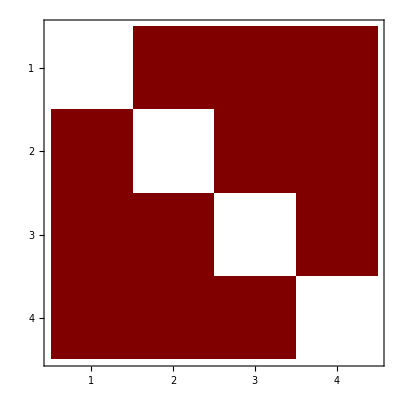

```mathematica
MatrixPlot[Normal[omega]]
```

```mathematica
omega//MatrixForm
```

(1)
 |  |  |  |

```mathematica
Coefficient[omega,h,0] //MatrixForm
```

(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

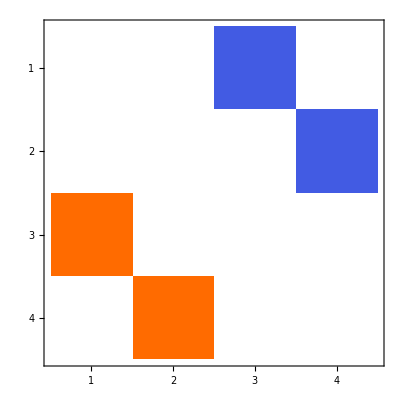

```mathematica
MatrixPlot[Coefficient[omega,h,0] ]
```

```mathematica
Simplify[Coefficient[omega,h,2]] //MatrixForm
```

(0 | 1/4 (x_2'[t] (a_(1,2)[1] U^(0,3)[x_1[t],x_2[t]]+(a_(1,1)[1]-a_(2,2)[1]) U^(1,2)[x_1[t],x_2[t]]-a_(1,2)[1] U^(2,1)[x_1[t],x_2[t]])+x_1'[t] (a_(1,2)[1] U^(1,2)[x_1[t],x_2[t]]+(a_(1,1)[1]-a_(2,2)[1]) U^(2,1)[x_1[t],x_2[t]]-a_(1,2)[1] U^(3,0)[x_1[t],x_2[t]])) | 1/6 (3 a_(1,2)[1] U^(1,1)[x_1[t],x_2[t]]+(-4+3 a_(1,1)[1]) U^(2,0)[x_1[t],x_2[t]]) | 1/12 (3 a_(1,2)[1] U^(0,2)[x_1[t],x_2[t]]+(-8+3 a_(1,1)[1]+3 a_(2,2)[1]) U^(1,1)[x_1[t],x_2[t]]+3 a_(1,2)[1] U^(2,0)[x_1[t],x_2[t]])
1/4 (x_2'[t] (-a_(1,2)[1] U^(0,3)[x_1[t],x_2[t]]+(-a_(1,1)[1]+a_(2,2)[1]) U^(1,2)[x_1[t],x_2[t]]+a_(1,2)[1] U^(2,1)[x_1[t],x_2[t]])+x_1'[t] (-a_(1,2)[1] U^(1,2)[x_1[t],x_2[t]]+(-a_(1,1)[1]+a_(2,2)[1]) U^(2,1)[x_1[t],x_2[t]]+a_(1,2)[1] U^(3,0)[x_1[t],x_2[t]])) | 0 | 1/12 (3 a_(1,2)[1] U^(0,2)[x_1[t],x_2[t]]+(-8+3 a_(1,1)[1]+3 a_(2,2)[1]) U^(1,1)[x_1[t],x_2[t]]+3 a_(1,2)[1] U^(2,0)[x_1[t],x_2[t]]) | 1/6 ((-4+3 a_(2,2)[1]) U^(0,2)[x_1[t],x_2[t]]+3 a_(1,2)[1] U^(1,1)[x_1[t],x_2[t]])
1/6 (-3 a_(1,2)[1] U^(1,1)[x_1[t],x_2[t]]+(4-3 a_(1,1)[1]) U^(2,0)[x_1[t],x_2[t]]) | 1/12 (-3 a_(1,2)[1] U^(0,2)[x_1[t],x_2[t]]+(8-3 a_(1,1)[1]-3 a_(2,2)[1]) U^(1,1)[x_1[t],x_2[t]]-3 a_(1,2)[1] U^(2,0)[x_1[t],x_2[t]]) | 0 | 0
1/12 (-3 a_(1,2)[1] U^(0,2)[x_1[t],x_2[t]]+(8-3 a_(1,1)[1]-3 a_(2,2)[1]) U^(1,1)[x_1[t],x_2[t]]-3 a_(1,2)[1] U^(2,0)[x_1[t],x_2[t]]) | 1/6 ((4-3 a_(2,2)[1]) U^(0,2)[x_1[t],x_2[t]]-3 a_(1,2)[1] U^(1,1)[x_1[t],x_2[t]]) | 0 | 0)

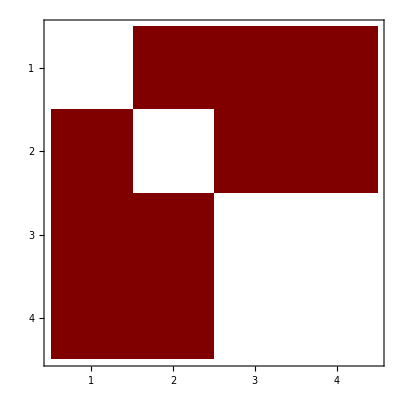

```mathematica
MatrixPlot[Coefficient[omega,h,2]]
```

```mathematica
Simplify[Coefficient[omega,h,4]] //MatrixForm
```

(1)
 |  |  |  |

```mathematica
MatrixPlot[Coefficient[omega,h,4]]
```

-Graphics-

#### Verification of reduced modified Hamiltonian system

```mathematica
omegaInv=Inverse[omega];
```

```mathematica
XHH =omegaInv.D[Normal @ HH,{q[[1;;2dim]]}];
```

```mathematica
(*O[h]^(o+1)+Simplify[O[h]^(o+1)+XHH - q[[dim+1;;3dim]]//.subsmthd]*)
```

```mathematica
FixedPoint[#/.ass/.subsmthd &,O[h]^(o+1)+XHH - q[[dim+1;;3dim]]]
```

{O[h]^5,O[h]^5,(-793/72 ⅇ^(2 x_1[t]+2 x_2[t]) (2 ⅇ^(x_1[t]+x_2[t])+x_1'[t]^2+2 x_1'[t] x_2'[t]+x_2'[t]^2)-113/288 ⅇ^(x_1[t]+x_2[t]) (122 ⅇ^(2 x_1[t]+2 x_2[t])-52 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2-122 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]-70 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)-743/120 ⅇ^(x_1[t]+x_2[t]) (16 ⅇ^(2 x_1[t]+2 x_2[t])+22 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+x_1'[t]^4+44 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+4 x_1'[t]^3 x_2'[t]+22 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2+6 x_1'[t]^2 x_2'[t]^2+4 x_1'[t] x_2'[t]^3+x_2'[t]^4)+1/24 (-122 ⅇ^(x_1[t]+x_2[t]) x_1'[t]-140 ⅇ^(x_1[t]+x_2[t]) x_2'[t]) (1/12 (-35 ⅇ^(x_1[t]+x_2[t]) x_1'[t]-35 ⅇ^(x_1[t]+x_2[t]) x_2'[t])+1/12 (26 ⅇ^(x_1[t]+x_2[t]) x_1'[t]+26 ⅇ^(x_1[t]+x_2[t]) x_2'[t]))+1/720 (-30393 ⅇ^(3 x_1[t]+3 x_2[t])+4458 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^4+19047 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^3 x_2'[t]+48440 ⅇ^(2 x_1[t]+2 x_2[t]) x_2'[t]^2+5673 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^4+3 ⅇ^(x_1[t]+x_2[t]) (-6754 ⅇ^(2 x_1[t]+2 x_2[t])+2567 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+6349 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+3782 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+3 ⅇ^(x_1[t]+x_2[t]) (-3377 ⅇ^(2 x_1[t]+2 x_2[t])+2567 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+6349 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+3782 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+x_1'[t] x_2'[t] (84730 ⅇ^(2 x_1[t]+2 x_2[t])+21477 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+x_1'[t]^2 (36290 ⅇ^(2 x_1[t]+2 x_2[t])+30393 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))-ⅇ^(x_1[t]+x_2[t]) (-34393/720 ⅇ^(2 x_1[t]+2 x_2[t])+1/240 (-11888 ⅇ^(2 x_1[t]+2 x_2[t])-4458 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2-8916 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]-4458 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)-179/120 (4 ⅇ^(2 x_1[t]+2 x_2[t])+ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+2 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/720 (24124 ⅇ^(2 x_1[t]+2 x_2[t])+6031 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+12062 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+6031 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+(-1061280 ⅇ^(2 x_1[t]+2 x_2[t])-2160 (6240 ⅇ^(2 x_1[t]+2 x_2[t])+1560 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+3120 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+1560 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/518400+(-1417680 ⅇ^(2 x_1[t]+2 x_2[t])-2040 (8400 ⅇ^(2 x_1[t]+2 x_2[t])+2100 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+4200 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+2100 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/518400)-ⅇ^(x_1[t]+x_2[t]) (-7327/180 ⅇ^(2 x_1[t]+2 x_2[t])+1/360 (-24124 ⅇ^(2 x_1[t]+2 x_2[t])-6031 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2-12062 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]-6031 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/120 (-15128 ⅇ^(2 x_1[t]+2 x_2[t])-5673 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2-11346 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]-5673 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/720 (-18904 ⅇ^(2 x_1[t]+2 x_2[t])-4726 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2-9452 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]-4726 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/120 (-11888 ⅇ^(2 x_1[t]+2 x_2[t])-4458 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2-8916 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]-4458 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)-67/60 (4 ⅇ^(2 x_1[t]+2 x_2[t])+ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+2 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/240 (11888 ⅇ^(2 x_1[t]+2 x_2[t])+4458 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+8916 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+4458 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/360 (18904 ⅇ^(2 x_1[t]+2 x_2[t])+4726 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+9452 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+4726 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/120 (15128 ⅇ^(2 x_1[t]+2 x_2[t])+5673 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+11346 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+5673 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/360 (24124 ⅇ^(2 x_1[t]+2 x_2[t])+6031 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+12062 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+6031 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+(-1061280 ⅇ^(2 x_1[t]+2 x_2[t])-2160 (6240 ⅇ^(2 x_1[t]+2 x_2[t])+1560 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+3120 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+1560 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/259200+(-1061280 ⅇ^(2 x_1[t]+2 x_2[t])-960 (6240 ⅇ^(2 x_1[t]+2 x_2[t])+1560 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+3120 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+1560 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/259200+(1061280 ⅇ^(2 x_1[t]+2 x_2[t])+960 (6240 ⅇ^(2 x_1[t]+2 x_2[t])+1560 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+3120 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+1560 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/518400+(1061280 ⅇ^(2 x_1[t]+2 x_2[t])+2160 (6240 ⅇ^(2 x_1[t]+2 x_2[t])+1560 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+3120 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+1560 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/259200+(-1417680 ⅇ^(2 x_1[t]+2 x_2[t])-2160 (8400 ⅇ^(2 x_1[t]+2 x_2[t])+2100 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+4200 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+2100 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/259200+(-1417680 ⅇ^(2 x_1[t]+2 x_2[t])-2040 (8400 ⅇ^(2 x_1[t]+2 x_2[t])+2100 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+4200 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+2100 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/259200+(1417680 ⅇ^(2 x_1[t]+2 x_2[t])+2040 (8400 ⅇ^(2 x_1[t]+2 x_2[t])+2100 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+4200 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+2100 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/259200+(1417680 ⅇ^(2 x_1[t]+2 x_2[t])+2160 (8400 ⅇ^(2 x_1[t]+2 x_2[t])+2100 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+4200 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+2100 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/518400)+x_2'[t] (16 ⅇ^(x_1[t]+x_2[t]) (1/12 (-35 ⅇ^(x_1[t]+x_2[t]) x_1'[t]-35 ⅇ^(x_1[t]+x_2[t]) x_2'[t])+1/12 (26 ⅇ^(x_1[t]+x_2[t]) x_1'[t]+26 ⅇ^(x_1[t]+x_2[t]) x_2'[t]))+35/6 ⅇ^(x_1[t]+x_2[t]) (1/12 (-26 ⅇ^(x_1[t]+x_2[t]) x_1'[t]-26 ⅇ^(x_1[t]+x_2[t]) x_2'[t])+1/12 (35 ⅇ^(x_1[t]+x_2[t]) x_1'[t]+35 ⅇ^(x_1[t]+x_2[t]) x_2'[t]))+1/720 (-4296 ⅇ^(2 x_1[t]+2 x_2[t]) x_1'[t]-358 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^3-4296 ⅇ^(2 x_1[t]+2 x_2[t]) x_2'[t]-1074 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2 x_2'[t]-1074 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]^2-358 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^3-1432 ⅇ^(x_1[t]+x_2[t]) (ⅇ^(x_1[t]+x_2[t]) x_1'[t]+ⅇ^(x_1[t]+x_2[t]) x_2'[t])-5315 (12 ⅇ^(2 x_1[t]+2 x_2[t]) x_1'[t]+ⅇ^(x_1[t]+x_2[t]) x_1'[t]^3+12 ⅇ^(2 x_1[t]+2 x_2[t]) x_2'[t]+3 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2 x_2'[t]+3 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]^2+ⅇ^(x_1[t]+x_2[t]) x_2'[t]^3+4 ⅇ^(x_1[t]+x_2[t]) (ⅇ^(x_1[t]+x_2[t]) x_1'[t]+ⅇ^(x_1[t]+x_2[t]) x_2'[t])))+1/720 (3216 ⅇ^(2 x_1[t]+2 x_2[t]) x_1'[t]+268 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^3+3216 ⅇ^(2 x_1[t]+2 x_2[t]) x_2'[t]+804 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2 x_2'[t]+804 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]^2+268 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^3+1072 ⅇ^(x_1[t]+x_2[t]) (ⅇ^(x_1[t]+x_2[t]) x_1'[t]+ⅇ^(x_1[t]+x_2[t]) x_2'[t])+4190 (12 ⅇ^(2 x_1[t]+2 x_2[t]) x_1'[t]+ⅇ^(x_1[t]+x_2[t]) x_1'[t]^3+12 ⅇ^(2 x_1[t]+2 x_2[t]) x_2'[t]+3 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2 x_2'[t]+3 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]^2+ⅇ^(x_1[t]+x_2[t]) x_2'[t]^3+4 ⅇ^(x_1[t]+x_2[t]) (ⅇ^(x_1[t]+x_2[t]) x_1'[t]+ⅇ^(x_1[t]+x_2[t]) x_2'[t]))))) h^4+O[h]^5,(-2135/144 ⅇ^(2 x_1[t]+2 x_2[t]) (2 ⅇ^(x_1[t]+x_2[t])+x_1'[t]^2+2 x_1'[t] x_2'[t]+x_2'[t]^2)-131/288 ⅇ^(x_1[t]+x_2[t]) (122 ⅇ^(2 x_1[t]+2 x_2[t])-52 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2-122 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]-70 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)-1891/240 ⅇ^(x_1[t]+x_2[t]) (16 ⅇ^(2 x_1[t]+2 x_2[t])+22 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+x_1'[t]^4+44 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+4 x_1'[t]^3 x_2'[t]+22 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2+6 x_1'[t]^2 x_2'[t]^2+4 x_1'[t] x_2'[t]^3+x_2'[t]^4)+1/24 (-104 ⅇ^(x_1[t]+x_2[t]) x_1'[t]-122 ⅇ^(x_1[t]+x_2[t]) x_2'[t]) (1/12 (-26 ⅇ^(x_1[t]+x_2[t]) x_1'[t]-26 ⅇ^(x_1[t]+x_2[t]) x_2'[t])+1/12 (35 ⅇ^(x_1[t]+x_2[t]) x_1'[t]+35 ⅇ^(x_1[t]+x_2[t]) x_2'[t]))+1/720 (-30393 ⅇ^(3 x_1[t]+3 x_2[t])+4458 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^4+19047 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^3 x_2'[t]+48440 ⅇ^(2 x_1[t]+2 x_2[t]) x_2'[t]^2+5673 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^4+3 ⅇ^(x_1[t]+x_2[t]) (-6754 ⅇ^(2 x_1[t]+2 x_2[t])+2567 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+6349 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+3782 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+3 ⅇ^(x_1[t]+x_2[t]) (-3377 ⅇ^(2 x_1[t]+2 x_2[t])+2567 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+6349 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+3782 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+x_1'[t] x_2'[t] (84730 ⅇ^(2 x_1[t]+2 x_2[t])+21477 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+x_1'[t]^2 (36290 ⅇ^(2 x_1[t]+2 x_2[t])+30393 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))-ⅇ^(x_1[t]+x_2[t]) (-34393/720 ⅇ^(2 x_1[t]+2 x_2[t])+1/240 (-15128 ⅇ^(2 x_1[t]+2 x_2[t])-5673 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2-11346 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]-5673 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)-67/60 (4 ⅇ^(2 x_1[t]+2 x_2[t])+ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+2 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/720 (18904 ⅇ^(2 x_1[t]+2 x_2[t])+4726 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+9452 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+4726 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+(-1061280 ⅇ^(2 x_1[t]+2 x_2[t])-960 (6240 ⅇ^(2 x_1[t]+2 x_2[t])+1560 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+3120 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+1560 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/518400+(-1417680 ⅇ^(2 x_1[t]+2 x_2[t])-2160 (8400 ⅇ^(2 x_1[t]+2 x_2[t])+2100 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+4200 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+2100 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/518400)-ⅇ^(x_1[t]+x_2[t]) (-2518/45 ⅇ^(2 x_1[t]+2 x_2[t])+1/720 (-24124 ⅇ^(2 x_1[t]+2 x_2[t])-6031 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2-12062 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]-6031 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/120 (-15128 ⅇ^(2 x_1[t]+2 x_2[t])-5673 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2-11346 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]-5673 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/360 (-18904 ⅇ^(2 x_1[t]+2 x_2[t])-4726 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2-9452 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]-4726 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/120 (-11888 ⅇ^(2 x_1[t]+2 x_2[t])-4458 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2-8916 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]-4458 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)-179/120 (4 ⅇ^(2 x_1[t]+2 x_2[t])+ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+2 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/120 (11888 ⅇ^(2 x_1[t]+2 x_2[t])+4458 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+8916 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+4458 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/360 (18904 ⅇ^(2 x_1[t]+2 x_2[t])+4726 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+9452 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+4726 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/240 (15128 ⅇ^(2 x_1[t]+2 x_2[t])+5673 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+11346 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+5673 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+1/360 (24124 ⅇ^(2 x_1[t]+2 x_2[t])+6031 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+12062 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+6031 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2)+(-1061280 ⅇ^(2 x_1[t]+2 x_2[t])-2160 (6240 ⅇ^(2 x_1[t]+2 x_2[t])+1560 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+3120 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+1560 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/259200+(-1061280 ⅇ^(2 x_1[t]+2 x_2[t])-960 (6240 ⅇ^(2 x_1[t]+2 x_2[t])+1560 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+3120 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+1560 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/259200+(1061280 ⅇ^(2 x_1[t]+2 x_2[t])+960 (6240 ⅇ^(2 x_1[t]+2 x_2[t])+1560 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+3120 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+1560 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/259200+(1061280 ⅇ^(2 x_1[t]+2 x_2[t])+2160 (6240 ⅇ^(2 x_1[t]+2 x_2[t])+1560 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+3120 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+1560 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/518400+(-1417680 ⅇ^(2 x_1[t]+2 x_2[t])-2160 (8400 ⅇ^(2 x_1[t]+2 x_2[t])+2100 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+4200 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+2100 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/259200+(-1417680 ⅇ^(2 x_1[t]+2 x_2[t])-2040 (8400 ⅇ^(2 x_1[t]+2 x_2[t])+2100 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+4200 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+2100 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/259200+(1417680 ⅇ^(2 x_1[t]+2 x_2[t])+2040 (8400 ⅇ^(2 x_1[t]+2 x_2[t])+2100 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+4200 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+2100 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/518400+(1417680 ⅇ^(2 x_1[t]+2 x_2[t])+2160 (8400 ⅇ^(2 x_1[t]+2 x_2[t])+2100 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2+4200 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]+2100 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^2))/259200)+x_1'[t] (61/6 ⅇ^(x_1[t]+x_2[t]) (1/12 (-26 ⅇ^(x_1[t]+x_2[t]) x_1'[t]-26 ⅇ^(x_1[t]+x_2[t]) x_2'[t])+1/12 (35 ⅇ^(x_1[t]+x_2[t]) x_1'[t]+35 ⅇ^(x_1[t]+x_2[t]) x_2'[t]))+1/720 (-3216 ⅇ^(2 x_1[t]+2 x_2[t]) x_1'[t]-268 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^3-3216 ⅇ^(2 x_1[t]+2 x_2[t]) x_2'[t]-804 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2 x_2'[t]-804 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]^2-268 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^3-1072 ⅇ^(x_1[t]+x_2[t]) (ⅇ^(x_1[t]+x_2[t]) x_1'[t]+ⅇ^(x_1[t]+x_2[t]) x_2'[t])-4190 (12 ⅇ^(2 x_1[t]+2 x_2[t]) x_1'[t]+ⅇ^(x_1[t]+x_2[t]) x_1'[t]^3+12 ⅇ^(2 x_1[t]+2 x_2[t]) x_2'[t]+3 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2 x_2'[t]+3 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]^2+ⅇ^(x_1[t]+x_2[t]) x_2'[t]^3+4 ⅇ^(x_1[t]+x_2[t]) (ⅇ^(x_1[t]+x_2[t]) x_1'[t]+ⅇ^(x_1[t]+x_2[t]) x_2'[t])))+1/720 (4296 ⅇ^(2 x_1[t]+2 x_2[t]) x_1'[t]+358 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^3+4296 ⅇ^(2 x_1[t]+2 x_2[t]) x_2'[t]+1074 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2 x_2'[t]+1074 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]^2+358 ⅇ^(x_1[t]+x_2[t]) x_2'[t]^3+1432 ⅇ^(x_1[t]+x_2[t]) (ⅇ^(x_1[t]+x_2[t]) x_1'[t]+ⅇ^(x_1[t]+x_2[t]) x_2'[t])+5315 (12 ⅇ^(2 x_1[t]+2 x_2[t]) x_1'[t]+ⅇ^(x_1[t]+x_2[t]) x_1'[t]^3+12 ⅇ^(2 x_1[t]+2 x_2[t]) x_2'[t]+3 ⅇ^(x_1[t]+x_2[t]) x_1'[t]^2 x_2'[t]+3 ⅇ^(x_1[t]+x_2[t]) x_1'[t] x_2'[t]^2+ⅇ^(x_1[t]+x_2[t]) x_2'[t]^3+4 ⅇ^(x_1[t]+x_2[t]) (ⅇ^(x_1[t]+x_2[t]) x_1'[t]+ⅇ^(x_1[t]+x_2[t]) x_2'[t]))))) h^4+O[h]^5}

```mathematica
Simplify[%]
```

{O[h]^5,O[h]^5,O[h]^5,O[h]^5}